```mathematica
Ejemplo 2
```

# Algoritmo Genetico Ejemplo 2

## Dibuja la superficie y los valores de cada generación

```mathematica
life[e_,f_,{ax_,bx_},{ay_,by_}]:=Module[{n,ptos,graph},
		n=Length[e[[1,1]]];
		ptos=Table[Join[e[[i,1,j]],{e[[i,2,j]]}],{i,1,genera},{j,1,n}];
	ptos=Table[Map[Point,ptos[[i]]],{i,1,genera}];
		graph=Plot3D[Evaluate[f[{x,y}]],{x,ax,bx},{y,ay,by},Mesh->False,PlotPoints->25,DisplayFunction->Identity];
			Table[Show[graph,	
	Graphics3D[{PointSize[0.05],ptos[[i]]}],
ViewPoint->{1.290, -3.262, 1.850},DisplayFunction->$DisplayFunction,AspectRatio->Automatic],{i,1,genera}]
];
```

## Dibuja el mejor valor de cada Generacion

```mathematica
exhibit[matr_]:=Module[{n},
		n=Length[matr];
	ListPlot[{Table[Last[matr[[i,2]]],{i,1,n}],
				Table[matr[[i,3]],{i,1,n}]},
				Joined->True,Frame->True,PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1]}]
				]
```

## Programa del Algoritmo Genetico

```mathematica
GA[Fobjetive_,{ax_,bx_},{ay_,by_},prec_,popsize_,pcross_,pmuta_,generate_]:=
	Module[{
			pop={},generacN=0,
	  newpop={},fitness={},
			notification={},
		evolution={},xsize,ysize,chromsize,xfactor,
       yfactor,finx,iniy,finy,
			meanfit,maxfit,best},
(*tamaño de c/var y factor de conversión*)
Size[{a_,b_},pre_]:=Ceiling[Log[2,(b-a)*pre]];fac[larg_,m_]:=N[larg/(2^m-1)];
		(*inicializacion poblac*)
birth[psize_,chsize_]:=
Partition[Table[Random[Integer],{chsize*psize}],chsize];
		(*decodificacion: entra chromosoma y sale el individuo*)
decode[chrom_]:=Module[{xx,yy},
				decim[gen_]:=gen.Reverse[(2^(#-1))& /@  Range[Length[gen]]];	xx= ax+decim[Take[chrom,{1,finx}]]*xfactor ;
		       yy=ay+decim[Take[chrom,{iniy,finy}]]*yfactor ; 
		Return[List[xx,yy]]
			];
		
		(*evalua un individuo de la forma apropiada
		fitForm[ind_]:=Module[{},*)
	
		          (*entra poblacion y sale lista: n mejores + sus ajustes + media geracional*)
			report[popul_,n_]:=Module[{majors,listfit,f,m,b},
					majors={decode[best]};
					listfit={maxfit};
					f=DeleteCases[fitness,maxfit];
					Do[m=Max[f];
						     b=First[Extract[popul,Position[f,m]]];
						    listfit=Join[{m},listfit];
						    majors=Join[{decode[b]},majors];
						   f=DeleteCases[f,m],
						{n-1}];
					meanfit=Plus@@fitness/popsize;
					Return[{majors,listfit,meanfit}]
				];
				(*Por el metodo "Remainder stochastic sampling with replacement"*)
	clones[popul_]:=Module [{ expected,remainder,acum,probwheel,wincopies,popaux},
		expected=fitness/meanfit ;
		popaux=Flatten[MapThread[Table[#1,{#2}]&,{popul,IntegerPart[expected]}],1];
	  probwheel=FractionalPart[ expected]/(Plus@@FractionalPart[expected]);
    acum=Rest[FoldList[Plus, 0.0, probwheel]];
    remainder=popsize-Length[popaux];
		wincopies=Table[(r=Random[]; i=1;Scan[If[#>r, Return[pop[[i]]], i++]&, acum]),
				{remainder}];
	 Flatten[List[popaux,wincopies],1]
		];
		(*entra poblac, se sortea segun pcross, los elegidos se aparean y se cruzan*)
		crossover[popnew_]:=Module[{mate,luck,children,popaux=popnew},	
		luck=Position[Table[Random[],{popsize}],r_/;r<pcross];
		If[OddQ[Length [luck]],luck=Rest[luck]];
		mate=Partition[Extract[popnew,luck],2];			
		children=Map[(j=Random[Integer,{1,(chromsize-1)}];
				List[Join[Take[#[[1]],j],Take[#[[2]],(j-chromsize)]],Join[Take[#[[2]],j],Take[#[[1]],(j-chromsize)]]])&,mate];
		children=Flatten[children,1];
		luck=Flatten[luck];
		Scan[(popaux[[luck[[#]]]]=children[[#]])& ,Range[Length[luck]]];
		Return[popaux]
		];
		(*Operador sobre los bits, y pmuta es deterministica*)
		mutation[popnew_]:=Module[{luck,tot=chromsize*popsize,popaux=popnew},
		luck=Table[Random[Integer,{1,tot}], {pmuta*tot}];
		popaux=Flatten[popaux];
		Scan[If[popaux[[#]]==0,popaux[[#]]=1,popaux[[#]]=0]&,luck];
		Return[Partition[popaux,chromsize]]		
		];		
		(* Main program *)	
      xsize=Size[{ax,bx},prec];
      ysize=Size[{ay,by},prec];
						chromsize=Plus@@{xsize,ysize};
       xfactor=fac[(bx-ax),xsize];
						yfactor=fac[(by-ay),ysize];
        finx=xsize; 
iniy=xsize+1;    finy=xsize+ysize;
		pop=birth[popsize,chromsize];
		generacN=1;
		While[generacN ≤ generate,
		Print[generacN];
	fitness=Map[Fobjetive[#]&,decode[#]&/@pop];
		maxfit=Max[fitness];
		best=First[Extract[pop,Position[fitness,maxfit]]];
         notification=report[pop,5];(*n mejores*)
			Print[notification];
		evolution=Join[evolution,{notification}];
		newpop=clones[pop];
		newpop=crossover[newpop];
		newpop=mutation[newpop];
		(*elitismo*) 
		newpop[[1]]=best;
		pop=newpop;
		generacN++;
		newpop={};
];
Return[evolution]
]
```

```mathematica
Fopt=Function[{u},u[[1]]^3+u[[2]]^3+9*u[[1]]^2-3*u[[2]]^2+15*u[[1]]-9*u[[2]]+1000];
 rangoX={-7,1};
 rangoY={-7,1};
	 precis=10^3;
psize=10;
pcro=0.25;
pmu=0.1;
genera=40;
sizeSave=5;
```

```mathematica
ev=GA[Fopt,rangoX,rangoY,precis,psize,pcro,
	pmu,genera];
```

1

{{{0.198144,-0.517763},{-5.14919,-6.82322},{-5.3289,0.430595},{-3.9049,-1.42901},{-3.9049,-1.42901}},{1007.05,1017.38,1019.96,1020.72,1022.93},951.089}

2

{{{-3.9049,-1.42901},{-1.45635,-3.8795},{-0.884996,-1.49738},{-3.9049,-1.42901},{-5.21853,0.0897326}},{1019.49,1022.78,1022.87,1022.93,1023.87},997.333}

3

{{{-5.21853,0.0897326},{-1.20242,-3.91076},{-5.21853,0.0897326},{-5.21853,0.0897326},{-4.76047,-0.53046}},{1020.94,1022.54,1022.75,1023.87,1028.45},977.534}

4

{{{-4.76047,-0.53046},{-5.3289,0.164937},{-5.3289,0.164937},{-4.76047,-0.53046},{-4.76047,-0.53046}},{1002.04,1005.04,1012.05,1022.75,1028.45},982.714}

5

{{{-5.3289,0.0418752},{0.295812,0.35246},{-4.82298,-2.77976},{-4.76047,-0.53046},{-4.76047,-0.53046}},{1005.17,1013.97,1014.75,1023.93,1028.45},991.871}

6

{{{-3.33354,-1.88023},{-3.33354,-1.88023},{-4.76047,-0.53046},{-3.38725,-2.1791},{-4.76047,-0.53046}},{1008.61,1012.2,1012.63,1017.95,1028.45},987.263}

7

{{{-4.76047,-0.53046},{-4.76047,-0.53046},{-4.82102,-2.03064},{0.35832,0.368087},{-4.76047,-0.53046}},{1002.91,1011.6,1017.78,1022.35,1028.45},954.483}

8

{{{-4.76047,-0.53046},{-4.76047,-0.53046},{-4.76047,-0.53046},{-0.836162,-2.15566},{-4.76047,-0.53046}},{988.609,1012.77,1017.63,1021.15,1028.45},950.268}

9

{{{-0.836162,-6.15615},{-4.76047,-0.53046},{-4.76047,-0.53046},{-0.836162,-6.15615},{-4.76047,-0.53046}},{992.494,1015.68,1016.22,1021.23,1028.45},933.285}

10

{{{-3.4566,0.32316},{-4.76047,-0.53046},{-4.76047,-0.53046},{-3.4566,0.32316},{-4.76047,-0.53046}},{997.96,1011.2,1016.32,1018.12,1028.45},935.575}

11

{{{-4.76047,-0.53046},{-4.76047,-0.53046},{-4.76047,-0.53046},{-0.264803,-4.24185},{-4.76047,-0.53046}},{998.97,1012.08,1016.48,1028.05,1028.45},960.816}

12

{{{-3.90587,0.0350385},{-1.80796,-2.58833},{-4.76047,-0.53046},{-1.80796,-2.58833},{-4.76047,-0.53046}},{993.64,1013.17,1018.81,1026.19,1028.45},949.128}

13

{{{-3.32182,-2.74069},{-2.45257,-3.46832},{-4.76047,-0.53046},{-1.80698,-2.49457},{-4.76047,-0.53046}},{1003.16,1005.63,1014.45,1027.04,1028.45},966.592}

14

{{{-3.32182,-2.73678},{-3.53083,-0.93383},{-2.93212,-2.36955},{-4.76047,-0.53046},{-4.76047,-0.53046}},{998.409,999.363,1015.21,1020.19,1028.45},964.38}

15

{{{-5.63558,-1.65071},{-4.76047,-0.53046},{-4.76047,-0.53046},{-6.93749,-2.25821},{-4.76047,-0.53046}},{1016.77,1016.77,1022.86,1024.5,1028.45},959.789}

16

{{{-6.81248,-1.27372},{-4.76047,-0.53046},{-4.76047,-0.53046},{-4.76047,-0.53046},{-5.23709,-1.13698}},{1009.32,1016.96,1024.07,1028.45,1029.53},961.409}

17

{{{-5.23709,-1.13698},{-5.23709,-1.13698},{-5.23709,-1.13698},{-5.23709,-1.13698},{-5.17458,-1.13698}},{1003.87,1007.47,1018.49,1029.53,1029.7},962.227}

18

{{{-6.81248,-1.27372},{-5.17458,-1.13698},{-5.17458,-1.13698},{-1.3831,0.382737},{-5.17458,-1.13698}},{1006.02,1013.76,1018.1,1020.27,1029.7},988.354}

19

{{{-5.17458,-1.13698},{-5.89928,0.574167},{-5.8104,-2.27384},{-5.89928,0.574167},{-5.17458,-1.13698}},{1013.45,1013.72,1019.34,1020.33,1029.7},1001.35}

20

{{{-5.77915,-2.39885},{-5.89147,-3.17629},{-5.89147,-3.17629},{-5.77915,-2.39885},{-5.17458,-1.13698}},{1003.7,1011.41,1019.31,1019.75,1029.7},995.214}

21

{{{-5.77915,-1.40068},{0.38176,-6.0868},{-5.17458,-1.13698},{0.433525,-2.48187},{-5.17458,-1.13698}},{965.972,967.747,996.846,1024.86,1029.7},911.334}

22

{{{-5.17458,-1.13698},{-5.77915,-1.40068},{-1.37627,-3.05421},{-1.56281,-2.23868},{-5.17458,-1.13698}},{988.616,996.768,997.949,1024.86,1029.7},936.922}

23

{{{-5.17458,-1.13698},{-5.17458,-1.13698},{-1.13014,-3.17824},{-2.57856,-2.24063},{-5.17458,-1.13698}},{959.296,997.873,1020.41,1024.51,1029.7},923.609}

24

{{{-1.13014,0.822244},{-1.13014,0.822244},{-1.13014,0.822244},{-2.56293,-6.24112},{-5.17458,-1.13698}},{997.334,1009.14,1009.27,1014.28,1029.7},929.619}

25

{{{-2.62837,-2.27677},{-5.17458,-1.13698},{-5.17458,-1.13698},{-1.0022,-4.01135},{-5.17458,-1.13698}},{997.272,997.73,1012.66,1016.55,1029.7},925.495}

26

{{{-5.9989,-3.90099},{-5.9989,-3.90099},{-5.9989,-3.90099},{-2.62837,-2.27677},{-5.17458,-1.13698}},{981.555,986.454,997.73,1015.19,1029.7},920.345}

27

{{{-2.69088,-2.26895},{0.977536,-2.2377},{-2.64791,0.822244},{-3.43707,-0.10365},{-5.17458,-1.13698}},{1013.71,1015.06,1018.11,1028.86,1029.7},1005.93}

28

{{{-5.38262,-2.85496},{-5.17458,-1.13698},{-5.80845,-0.0577463},{-5.17458,-1.13698},{-5.17458,-1.13698}},{1002.37,1003.28,1015.06,1021.06,1029.7},1003.05}

29

{{{-3.30814,-0.061653},{-5.17458,-1.13698},{-5.17458,-1.13698},{-3.30814,-0.061653},{-5.17458,-1.13698}},{1009.35,1010.5,1013.21,1013.91,1029.7},983.532}

30

{{{-5.17458,-1.13698},{-3.02198,-1.1194},{-5.17458,-1.13698},{-5.17458,-1.13698},{-5.17458,-1.13698}},{1010.44,1010.56,1014.18,1024.94,1029.7},999.625}

31

{{{-5.17458,-1.13698},{-5.30839,0.939446},{-5.17458,-1.13698},{-5.30839,0.939446},{-5.17458,-1.13698}},{1010.35,1010.64,1014.13,1029.21,1029.7},1007.73}

32

{{{-2.65181,-1.27665},{0.978513,-5.68441},{0.978513,-5.68441},{0.978513,-5.68441},{-5.17458,-1.13698}},{1000.28,1009.38,1010.73,1020.18,1029.7},946.221}

33

{{{-6.85545,-0.901599},{-5.17458,-1.13698},{0.702112,-1.0608},{-5.64534,-2.95165},{-5.17458,-1.13698}},{1009.42,1020.29,1026.7,1027.29,1029.7},948.287}

34

{{{-5.17458,-1.13698},{-5.64534,-2.20156},{0.702112,-1.02173},{-5.64534,-2.20156},{-5.17458,-1.13698}},{1020.31,1021.06,1026.5,1027.24,1029.7},974.523}

35

{{{-5.91295,-0.452326},{-5.64534,-2.20156},{0.00183128,-6.37395},{-5.64534,-2.20156},{-5.17458,-1.13698}},{1016.84,1021.06,1022.6,1024.91,1029.7},949.304}

36

{{{-2.73288,0.36711},{-0.435722,-0.952387},{-5.64534,-2.01404},{-0.432792,-1.60969},{-5.17458,-1.13698}},{1020.02,1022.36,1025.18,1025.62,1029.7},1014.9}

37

{{{-5.53791,-0.729703},{-5.17458,-1.13698},{-1.67611,-4.01428},{-4.27017,-0.814675},{-5.17458,-1.13698}},{1007.22,1018.18,1026.99,1027.69,1029.7},951.866}

38

{{{-5.17458,-1.13698},{-6.60835,0.467708},{-1.53742,-0.167135},{-5.17458,-1.13698},{-5.17458,-1.13698}},{1000.56,1001.06,1007.22,1024.94,1029.7},925.294}

39

{{{-0.301917,0.244048},{-6.55756,0.467708},{-5.86705,-0.868392},{-5.17458,-1.13698},{-5.17458,-1.13698}},{1004.93,1007.34,1013.6,1024.74,1029.7},998.496}

40

{{{-1.36552,-0.618362},{-6.55854,0.463802},{-6.43157,0.348553},{-6.55854,0.463802},{-5.17458,-1.13698}},{1001.92,1006.31,1009.12,1014.13,1029.7},966.118}

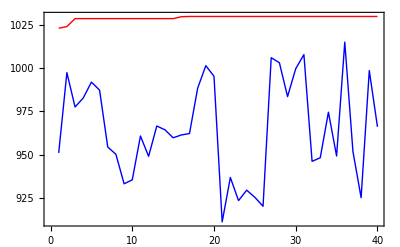

```mathematica
exhibit[ev]
```

```mathematica
life[ev,Fopt,rangoX,rangoY]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(* El maximo ocurre en (-5,-1), y el valor máximo es 1030
El criterio de la segunda derivada y los algoritmos geneticos
coinciden en los resultados *)
```